```mathematica
Clear[p,q,r]
```

(p∨q)∧(¬p∧¬q)

```mathematica
FullForm[(p∨q)∧(¬p∧¬q)]/.{Or->or,And->and,Not->not}
```

and[or[p,q],not[p],not[q]]

## lets just see if we can break at the ANDs

```mathematica
and[or[p,q],not[p],not[q]]/.{and->List}
```

```mathematica
lis={or[p,q],not[p],not[q]}
```

{or[p,q],not[p],not[q]}

## iterate down the list, using TREE RULES

If you then apply AND to the final lists, you get F

-Graphics-

We then use the or distributive rule

```mathematica
distribute[expr_]:=Module[{},
orlist={};
elselist={};
orlist=(Cases[expr,or[a__]->List[a]]);
elselist=(Cases[expr,not[a_]->a]);
Join[orlist,elselist]]
distribute[lis]
```

{{p,q},p,q}

```mathematica
copyTruthTreeFormat
```

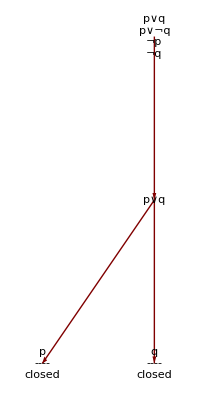

```mathematica
Clear[p,q,r,description,root];
forma=ToString[TraditionalForm@Grid[#]]&;
description={forma[{{(p∨q)},{(p∨¬q)},{¬p},{¬q}}]->forma[{{(p∨q)}}],forma[{{(p∨q)}}]->forma[{{p},{"----"},{"closed"}}],forma[{{(p∨q)}}]->forma[{{q},{"----"},{"closed"}}]};

LayeredGraphPlot[description,Automatic,root=forma[{{(p∨q)},{¬p},{¬q}}];
VertexLabeling->True]
```